Sample (C1,C2) = (0.5,0.5): {{0.1,-8.60334},{0.11,-7.81839},{0.12,-7.1697},{0.13,-6.62516},{0.14,-6.16196}}

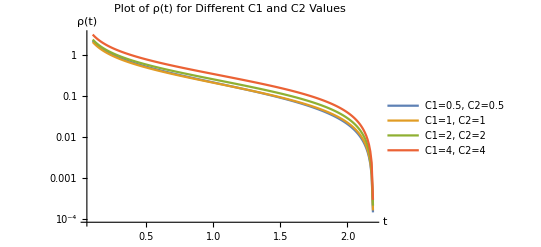

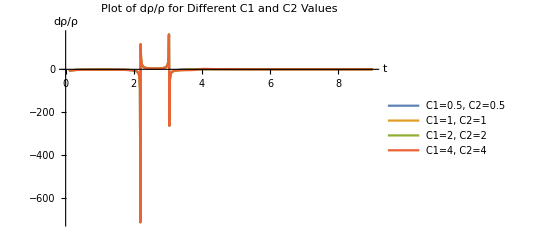

```mathematica
ClearAll["Global`*"]

(*Define constants*)
c=1;
p=2;
plj=10;
t0=10^-1;(*0.1*)(*Define the rho function*)rho[t_,C1_,C2_]:=((1+(1/2)*(p*t)^(2/3))*c)/Sqrt[C1*(t/t0)^2]*Sqrt[c^4+(C2+C1*t*(1-(3/5)*(p*t)^(2/3)))^2];
rho[t_,C1_,C2_]:=(c*(Cos[(plj*t)^(1/3)]+(plj*t)^(1/3)*Sin[(plj*t)^(1/3)])/Sqrt[C1*(t/t0)^2])*Sqrt[c^4+(C2+C1*(-3*(plj*Cos[(plj*t)^(1/3)]*t^(1/3)-(plj)^(2/3)*Sin[(plj*t)^(1/3)])/((plj^2)*Sin[(plj*t)^(1/3)]*t^(1/3)+p^(5/3)*Cos[(plj*t)^(1/3)])))^2];

(*Define drho*)
drho[t_?NumericQ,C1_?NumericQ,C2_?NumericQ]:=Evaluate[D[rho[x,C1,C2],x]]/. x->t//N

C1List={0.5,1,2,4};
C2List={0.5,1,2,4};

(*Define the range and step for t*)
tList=Range[t0,9,0.01];

(*Compute rho(t) data for each pair of C1 and C2*)
dataRho=Table[Table[{t,rho[t,C1List[[i]],C2List[[i]]]},{t,tList}],{i,Length[C1List]}];

(*Compute drho/rho data for each pair of C1 and C2*)
dataDrhoOverRho=Table[Module[{valRho,valDrho,ratio},Table[valRho=rho[t,C1List[[i]],C2List[[i]]];
valDrho=drho[t,C1List[[i]],C2List[[i]]];
ratio=If[valRho!=0,valDrho/valRho,Indeterminate];
{t,ratio},{t,tList}]],{i,Length[C1List]}];

(*Check a few sample points to ensure they're not empty or indeterminate*)
Print["Sample (C1,C2) = (0.5,0.5): ",Take[dataDrhoOverRho[[1]],5]];

labels=Table["C1="<>ToString[C1List[[i]]]<>", C2="<>ToString[C2List[[i]]],{i,Length[C1List]}];

(*Plot rho(t)*)
rhoPlot=ListLinePlot[dataRho,PlotLegends->labels,AxesLabel->{"t","ρ(t)"},PlotLabel->"Plot of ρ(t) for Different C1 and C2 Values",PlotStyle->Thick,PlotRange->All,ScalingFunctions->{"Linear","Log"}];

(*Plot (d\rho/\rho)(t)*)
drhoOverRhoPlot=ListLinePlot[dataDrhoOverRho,PlotLegends->labels,AxesLabel->{"t","dρ/ρ"},PlotLabel->"Plot of dρ/ρ for Different C1 and C2 Values",PlotStyle->Thick,PlotRange->All];

rhoPlot
drhoOverRhoPlot
```